```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Wed 29 Mar 2023 08:37:56

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

6.0.2 (June 28, 2021)

## Lecture 08 edited by Chi-Ok Hwang, originally made by Dr. 전 경원

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

MathSymbolica Package

Winners of Wolfram Innovator Award 2017

-Graphics-

### How to Install SymbolicCoputing Package

```mathematica
ToExpression[URLFetch["https://symbcomp.gist.ac.kr/downloads/InstallSymbComp.m"]]
```

## Precalculus

Solving simultaneous equations

```mathematica
ClearAll["Global`*"]
Solve[{{3,1},{2,-5}}.{x,y}=={7,8},{x,y}]
Solve[{x+y==3,x-y==1},{x,y}]
```

{{x→43/17,y→-10/17}}

{{x→2,y→1}}

```mathematica
Solve[{a x+b y==e,c x-d y==f},{x,y}]
```

{{x→-(-d e-b f)/(b c+a d),y→-(-c e+a f)/(b c+a d)}}

```mathematica
Solve[{x^2+y^2==1,x+y==a},{x,y}]
```

{{x→1/2 (a-√(2-a^2)),y→1/2 (a+√(2-a^2))},{x→1/2 (a+√(2-a^2)),y→1/2 (a-√(2-a^2))}}

```mathematica
{{x->1/2 (a-√(2-a^2)),y->1/2 (a+√(2-a^2))},{x->1/2 (a+√(2-a^2)),y->1/2 (a-√(2-a^2))}}
```

{{x→1/2 (a-√(2-a^2)),y→1/2 (a+√(2-a^2))},{x→1/2 (a+√(2-a^2)),y→1/2 (a-√(2-a^2))}}

```mathematica
Solve[{x^2+y^2==1,x+y==0.7},{x,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.26441,y→0.96441},{x→0.96441,y→-0.26441}}

```mathematica
x^3+y^4/.%/.a->0.7
```

{0.846577,0.901873}

```mathematica
a=0.7;
x=1/2 (a-√(2-a^2));
y=1/2 (a+√(2-a^2));
x^3+y^4
x=1/2 (a+√(2-a^2));
y=1/2 (a-√(2-a^2));
x^3+y^4
```

0.846577

0.901873

```mathematica
{{3,1},{2,-5}}.{x,y}=={7,8}
```

{3 x+y,2 x-5 y}=={7,8}

```mathematica
{{3,1},{2,-5}}.{x,y}=={7,8};
Solve[%,{x,y}]
```

{{x→43/17,y→-10/17}}

```mathematica
LogicalExpand[%%]
```

False

## Motivating a Need for Limits

Demonstration: Archimedes’ Approximation of Pi

Set the number of sides equal to 3, and calculate the area of inscribed triangle.

Using the fact that the angle of the center is divided into 6 pieces.

```mathematica
S==3 1/2"height""base"
SCMAF[%,RA,{At[2],{"height"->Cos[30°],"base"->2Sin[30°]}}]
```

S==(3 base height)/2

S==(3 √3)/4

Set the number of sides equal to 6, and calculate the area of inscribed hexagon.

```mathematica
S==6 1/2"height""base"
SCMAF[%,RA,{At[2],{"height"->Cos[360/12°],"base"->2Sin[360/12°]}}]
```

S==3 base height

S==(3 √3)/2

Determine a general function that will find the area of the inscribed regular n sided polygon.

```mathematica
S==n 1/2"height""base"
SCMAF[%,RA,{At[2],{"height"->Cos[(2π)/(2n)],"base"->2Sin[(2π)/(2n)]}},
FullSimplify,At[2]]
```

S==(base height n)/2

S==n Cos[π/n] Sin[π/n]

S==n/2 Sin[(2 π)/n]

For n=3,

```mathematica
S==n/2 Sin[(2 π)/n]/.n->3
```

S==(3 √3)/4

For n=6,

```mathematica
S==n/2 Sin[(2 π)/n]/.n->6
```

S==(3 √3)/2

For n=200,

```mathematica
S==n/2 Sin[(2 π)/n]
SCMAF[%,RA,{At[2],n->200},
N,At[2]]
```

S==n/2 Sin[(2 π)/n]

S==100 Sin[π/100]

S==3.14108

For n→∞,

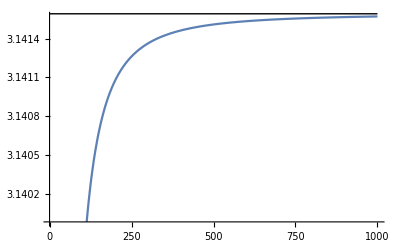

```mathematica
Plot[n/2 Sin[(2 π)/n],{n,3,1000},Epilog->{Style[Line[{{0,π},{1000,π}}],Dotted,Red]}]
```

```mathematica
Limit[n/2 Sin[(2 π)/n],n->∞]
```

π

Or using MathSymbolica,

```mathematica
SCARA[Underscript[Limit, n->∞][S],S==n/2 Sin[(2 π)/n]]
SCMAF[%,SCEvalLimit,At[2]]
```

Limit_(n→∞)[S]==Limit_(n→∞)[n/2 Sin[(2 π)/n]]

Limit_(n→∞)[S]==Limit_(n→∞)[n/2 Sin[(2 π)/n]]

## Practice

```mathematica
(*  ReplaceALl *)
3 1/2"height""base"/.{"height"->Cos[30°],"base"->2Sin[30°]}
```

(3 √3)/4

```mathematica
S==3 1/2"height""base"
SCMAF[%,RA,{At[2],{"height"->Cos[30°],"base"->2Sin[30°]}}]
```

S==(3 base height)/2

S==(3 √3)/4

```mathematica
SCARA[x+y,x==1]
```

x+y==1+y

```mathematica
SCARA[{x,y},{x==1,y==2}]//Thread
```

{x==1,y==2}

```mathematica
SCARA[x-Subscript[x, 1],{Subscript[x, 1]==y,x==z}]
```

x-x_1==-y+z

Schematic picture for π value using chords summation

-Graphics-Figure: Geometry of a sector with radius of 1, height α, chords x_n and x_(n+1)

Applying Phthagorean theorem on ΔABC

```mathematica
<<Notation`
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]                                (* To use variables with subscripts! *)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(Subscript[x, n]/2)^2+α^2==1
SCMAF[%,SCSolve,{All,α, Assumptions->{α>0}}]
```

x_n^2/4+α^2==1

{}

Applying Phthagorean theorem on ΔBCD

```mathematica
(1-α)^2+(Subscript[x, n]/2)^2==Subscript[x, n+1]^2
SCMAF[%,RA, {At[1],{α-> 1/2 √(4-Subscript[x, n]^2)}},SCSolve,{All,Subscript[x, n+1]}, Assumptions-> {Subscript[x, n]>0,Subscript[x, n+1]>0, α>0},RA,{At[3],{α-> 1/2 √(4-Subscript[x, n]^2)}}]
```

x_n^2/4+(1-α)^2==(x_(n+1))^2

```mathematica
Assumptions[{{Subscript[x, n+1]==-√(2-√(4-Subscript[x, n]^2))},{Subscript[x, n+1]==√(2-√(4-Subscript[x, n]^2))}},Subscript[x, n]>0,Subscript[x, n+1]>0,α>0]
```

```mathematica
Assumptions[{{Subscript[x, n+1]==-√(2-√(4-Subscript[x, n]^2))},{Subscript[x, n+1]==√(2-√(4-Subscript[x, n]^2))}},Subscript[x, n]>0,Subscript[x, n+1]>0,α>0]
```

Assumptions[{{x_(n+1)==-√(2-√(4-x_n^2))},{x_(n+1)==√(2-√(4-x_n^2))}},x_n>0,x_(n+1)>0,α>0]

```mathematica
Assumptions[{{Subscript[0.9644102863722254, 1+n]==-√(2-√(4-Subscript[0.9644102863722254, n]^2))},{Subscript[0.9644102863722254, 1+n]==√(2-√(4-Subscript[0.9644102863722254, n]^2))}},Subscript[0.9644102863722254, n]>0,Subscript[0.9644102863722254, 1+n]>0,α>0]
```

Assumptions[{{0.96441_(1+n)==-√(2-√(4-(0.96441_n)^2))},{0.96441_(1+n)==√(2-√(4-(0.96441_n)^2))}},0.96441_n>0,0.96441_(1+n)>0,α>0]

Symbol::symname: The string "0⎵Dot⎵9644102863722254⎵Backquote⎵Subscript⎵1⎵Plus⎵n" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

Symbol::symname: The string "0⎵Dot⎵9644102863722254⎵Backquote⎵Subscript⎵n" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

```mathematica
Assumptions[{{Subscript[0.9644102863722254, 1+n]==-√(2-√(4-Subscript[0.9644102863722254, n]^2))},{Subscript[0.9644102863722254, 1+n]==√(2-√(4-Subscript[0.9644102863722254, n]^2))}},Subscript[0.9644102863722254, n]>0,Subscript[0.9644102863722254, 1+n]>0,α>0]
```

Assumptions[{{0.96441_(1+n)==-√(2-√(4-(0.96441_n)^2))},{0.96441_(1+n)==√(2-√(4-(0.96441_n)^2))}},0.96441_n>0,0.96441_(1+n)>0,α>0]

```mathematica
RSolve[{a[n]==√(2-√(4-a[n-1]^2)),a[1]==√2},a[n],n]
```

RSolve[{a[n]==√(2-√(4-a[-1+n]^2)),a[1]==√2},a[n],n]

```mathematica
ClearAll["Global`*"]
k=100;
RecurrenceTable[{a[n+1]==N[√(2-√(4-a[n]^2)),k],a[1]==√2},a,{n,1,k}];
Take[%,-1] 2^k
N[π,k]-%
```

{3.141592653589793238462643383279502884197}

{0.}

◼ SCLimit has the same syntax as the built-in function Limit; however, it does not evaluate the limit.
◼   Limits expressed using SCLimit can be evaluated using SCEvalLimit.

```mathematica
a[n_]=2 Sin[Pi/2^(n+1)]   
Limit[2^n a[n],n-> Infinity]
```

2 Sin[2^(-1-n) π]

π

```mathematica
a[n_]:=2 Sin[Pi/2^(n+1)]   
Limit[2^n a[n],n-> Infinity]
```

π

## Expand, There is no SCExpand command.

```mathematica
Expand[(1+x)^10]
```

1+10 x+45 x^2+120 x^3+210 x^4+252 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10

```mathematica
SCExpand[(1+x)^10]
```

SCExpand[(1+x)^10]

```mathematica
Expand[(1+x+y) (2-x)^3]
```

8-4 x-6 x^2+5 x^3-x^4+8 y-12 x y+6 x^2 y-x^3 y

```mathematica
Expand[(1+x)^10]
```

1+10 x+45 x^2+120 x^3+210 x^4+252 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10

```mathematica
Expand[(1+x)^10,Modulus->2]
```

1+x^2+x^8+x^10

```mathematica
Expand[(1+x)^3,Modulus->2]
```

1+x+x^2+x^3

```mathematica
Column[Table[CoefficientList[Expand[(1+x)^t,Modulus->2],x],{t,0,31}]]
```

{1}
{1,1}
{1,0,1}
{1,1,1,1}
{1,0,0,0,1}
{1,1,0,0,1,1}
{1,0,1,0,1,0,1}
{1,1,1,1,1,1,1,1}
{1,0,0,0,0,0,0,0,1}
{1,1,0,0,0,0,0,0,1,1}
{1,0,1,0,0,0,0,0,1,0,1}
{1,1,1,1,0,0,0,0,1,1,1,1}
{1,0,0,0,1,0,0,0,1,0,0,0,1}
{1,1,0,0,1,1,0,0,1,1,0,0,1,1}
{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}
{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}
{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}
{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1}
{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,1}
{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1}
{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1}
{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1}
{1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1}
{1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1}
{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,1}
{1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1}
{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1}
{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Expand[Sin[x+y],Trig->True]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

## Series

```mathematica
Series[Exp[x],{x,0,4}]
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

```mathematica
Series[Exp[x],{x,1,4}]
```

ⅇ+ⅇ (x-1)+1/2 ⅇ (x-1)^2+1/6 ⅇ (x-1)^3+1/24 ⅇ (x-1)^4+O[x-1]^5

```mathematica
Series[f[x],{x,0,3}]
```

f[0]+f'[0] x+1/2 f''[0] x^2+1/6 f'''[0] x^3+O[x]^4

```mathematica
Series[Exp[x y],{x,0,3},{y,0,3}]
```

```mathematica
1+(y+O[y]^4) x+x^2 y^2/2+O[y]^4+x^3 y^3/6+O[y]^4+O[x]^4
SCSeries[Exp[x],{x,0,4}]
```

1+(y+O[y]^4) x+x^2 y^2/2+O[y]^4+x^3 y^3/6+O[y]^4+O[x]^4

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

```mathematica
SCSeries[f[x],{x,0,3}]
```

f[0]+f'[0] x+1/2 f''[0] x^2+1/6 f'''[0] x^3+O[x]^4

```mathematica
SCSeries[Exp[x y],{x,0,3},{y,0,3}]
```

1+(y+O[y]^4) x+x^2 y^2/2+O[y]^4+x^3 y^3/6+O[y]^4+O[x]^4